```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\neural-networks-tasks

```mathematica
Dimensions[Data=]
```

```mathematica
Data=Import["NG23T04Problem.xlsx",{"Sheets","Шпак Андрей"}]
```

```mathematica
Map[Dimensions,{Train,Test}=Partition[RandomSample@Data,UpTo[0.8*Length[Data]]]]
```

{{2400,3},{600,3}}

```mathematica
pts=Flatten[{Point[{#[[1]],#[[2]]}],If[#[[3]]==-1.,Red,Blue]}&/@Train]
```

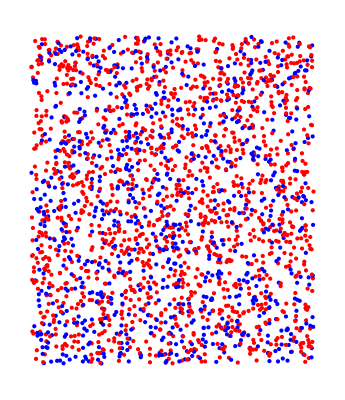

```mathematica
Graphics[{pts}]
```

# NG^23 T_04. Метод k-средних и RBF-сети

04-фев-2023
Шпак Андрей

## Section. Обучающий и тестирующий наборы

```mathematica
SetDirectory[NotebookDirectory[]]
Dimensions[Data=Import["NG23T04Problem.xlsx",{"Sheets","Шпак Андрей"}]]
```

D:\neural-networks-tasks

{3000,3}

```mathematica
Map[Dimensions,{Train,Test}=Partition[RandomSample@Data,UpTo[0.8*Length[Data]]]]
```

{{2400,3},{600,3}}

```mathematica
Map[Dimensions,{TrainX=Train[[All,{1,2}]],TrainY=Rationalize@Train[[All,3]]}]
Map[Dimensions,{TestX=Train[[All,{1,2}]],TestY=Rationalize@Train[[All,3]]}]
```

{{2400,2},{2400}}

{{2400,2},{2400}}

```mathematica
Length[iBlue=Flatten@Position[TrainY,+1]]
Length[iRed=Flatten@Position[TrainY,-1]]
%%+%
```

887

1513

2400

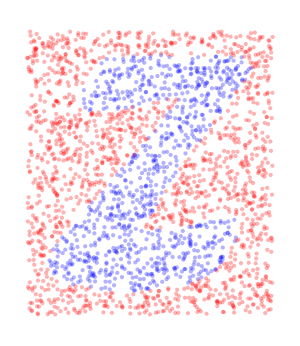

```mathematica
Fig0=Graphics[{PointSize@Medium,Opacity@.3,
Blue,Point@TrainX[[iBlue]],
Red,Point@TrainX[[iRed]]},
AspectRatio->Automatic,ImageSize->300]
```

## Section. Метод k-средних

Для начала решил взять небольшой список точек и проверить свои действия на нем.

```mathematica
test2={{98,62},{80,95},{71,130},{89,164},{137,115},{107,155},{109,105},{174,62},{183,115},{164,153},{142,174},{140,80},{308,123},{229,171},{195,237},{180,298},{179,340},{251,262},{300,176},{346,178},{311,237},{291,283},{254,340},{215,308},{239,223},{281,207},{283,156}}
```

{{98,62},{80,95},{71,130},{89,164},{137,115},{107,155},{109,105},{174,62},{183,115},{164,153},{142,174},{140,80},{308,123},{229,171},{195,237},{180,298},{179,340},{251,262},{300,176},{346,178},{311,237},{291,283},{254,340},{215,308},{239,223},{281,207},{283,156}}

Взял два набора кластеров, выбрал случайным образом центры, подготовил список, в котором лежат центры кластеров и будут добавляться другие точки.

```mathematica
n=2;
pts=RandomSample[test2,n];
clasters=Partition[pts,1]
```

{{{229,171}},{{254,340}}}

Решил убрать центры точек, взятые случано выше для списка, из которого буду с помощью Nearest добавлять точки, ближайшие каждому центру .

```mathematica
remainPts=Delete[test2,Flatten@Position[test2,pts[[#]]]&/@Range[1,n]]
```

{{98,62},{80,95},{71,130},{89,164},{137,115},{107,155},{109,105},{174,62},{183,115},{164,153},{142,174},{140,80},{308,123},{195,237},{180,298},{179,340},{251,262},{300,176},{346,178},{311,237},{291,283},{215,308},{239,223},{281,207},{283,156}}

Пока список, из которого я беру каждую новую точку и отправляю в набор к кластеру, не окажется пустым, я прохожусь по каждому из центров и добавляю к нему ближайшую точку .

```mathematica
While[Length@remainPts!=0,
For[i=1,i<=n,i++,
clasters[[i]]=Append[clasters[[i]],lstPt=Flatten@Nearest[remainPts,clasters[[i,-1]]]];
remainPts=Delete[remainPts,Flatten@Position[remainPts,lstPt]];
If[Length@remainPts==0,Break[],None];
]
]
```

```mathematica
clasters
```

{{{229,171},{239,223},{251,262},{291,283},{311,237},{281,207},{300,176},{283,156},{308,123},{346,178},{174,62},{140,80},{98,62},{107,155}},{{254,340},{215,308},{180,298},{179,340},{195,237},{142,174},{164,153},{183,115},{137,115},{109,105},{80,95},{71,130},{89,164}}}

```mathematica
remainPts=test2;
```

```mathematica
For[i=1,i<=n,i++,
tmpCentroid=Plus@@clasters[[i]]/Length[clasters[[i]]];
clasters[[i]]=Nearest[remainPts,tmpCentroid];
remainPts=Delete[remainPts,Flatten@Position[remainPts,clasters[[i]]]];
]
```

```mathematica
clasters
```

{{{229,171}},{{142,174}}}

```mathematica
getClasters[n_,Data_]:=Block[{pts,clasters,remainPts},
pts=RandomSample[Data,n];
clasters=Partition[pts,1];
tmpClasters={};
remainPts=Delete[Data,Flatten@Position[Data,pts[[#]]]&/@Range[1,n]];
While[True,
While[Length@remainPts!=0,
For[i=1,i<=n,i++,
clasters[[i]]=Append[clasters[[i]],lstPt=Flatten@Nearest[remainPts,clasters[[i,-1]]]];
remainPts=Delete[remainPts,Flatten@Position[remainPts,lstPt]];
If[Length@remainPts==0,Break[],None];
]
];
If[clasters==tmpClasters,Return[clasters];Break[],tmpClasters=clasters];
remainPts=Data;
For[i=1,i<=n,i++,
tmpCentroid=Plus@@clasters[[i]]/Length[clasters[[i]]];
clasters[[i]]=Nearest[remainPts,tmpCentroid];
remainPts=Delete[remainPts,Flatten@Position[remainPts,clasters[[i]]]];
];
]
]
```

```mathematica
tmpClsrs=getClasters[2,test2]
```

{{{137,115},{137,115},{109,105},{80,95},{71,130},{89,164},{107,155},{142,174},{164,153},{183,115},{174,62},{140,80},{98,62},{229,171},{195,237}},{{251,262},{251,262},{239,223},{281,207},{300,176},{283,156},{308,123},{346,178},{311,237},{291,283},{254,340},{215,308},{180,298},{179,340}}}

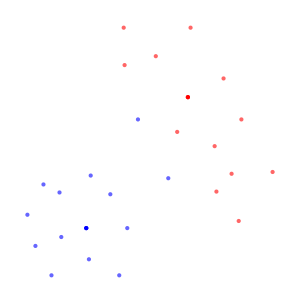

```mathematica
Fig1=Graphics[{PointSize@Medium,Opacity@.6,
Blue,Point@tmpClsrs[[1]],
Red,Point@tmpClsrs[[2]],
Opacity@1,Red,Point@tmpClsrs[[2,1]],Blue,Point@tmpClsrs[[1,1]]},
AspectRatio->Automatic,ImageSize->300]
```

```mathematica
getClasters[20,TrainX[[iBlue]]]
```

## Section. Зоны влияния

## Section. Радиально-базисные функции

## Section. Псевдообратная матрица

## Section. Сеть радиально-базисных функций

## Section. Ошибки первого и второго рода

## Section. Зависимость качества классификатора от размера зоны влияния RBF